```mathematica
SetDirectory["/home/kamano/gitsrc/ChemicalStructureRecognition"]
```

/home/kamano/gitsrc/ChemicalStructureRecognition

## Images

```mathematica
cdata=ChemicalData[];
```

```mathematica
ldata=Length[cdata]
```

44089

### create test

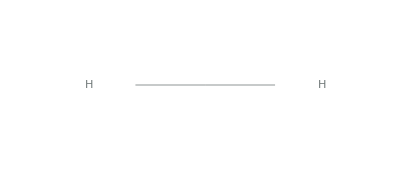

```mathematica
ChemicalData[cdata[[1]]]
```

```mathematica
r[1]=Rasterize[ChemicalData[cdata[[1]]],RasterSize->300,ImageSize->100]
```

-Graphics-

```mathematica
Information[r[1]]
```

Image

```mathematica
br[1]=Binarize[r[1]]
```

-Graphics-

```mathematica
(*Export["OSRA-test/br1.jpg",br[1]]*)
```

OSRA-test/br1.jpg

```mathematica
s=ChemicalData[cdata[[1]],"SMILES"]
```

[HH]

### random selection

```mathematica
len=50
```

50

```mathematica
rs={39628,8924,5540,37508,38397,43288,30646,2945,29820,32286,28281,17023,11401,9910,15290,16933,35978,40439,15657,32027,19707,7486,13838,5810,16301,21714,7405,27756,8595,15397,24766,23711,13509,34262,28913,20008,26901,21734,37166,38012,3040,43691,13235,37832,17538,17242,1661,1989,12604,5184}
```

{39628,8924,5540,37508,38397,43288,30646,2945,29820,32286,28281,17023,11401,9910,15290,16933,35978,40439,15657,32027,19707,7486,13838,5810,16301,21714,7405,27756,8595,15397,24766,23711,13509,34262,28913,20008,26901,21734,37166,38012,3040,43691,13235,37832,17538,17242,1661,1989,12604,5184}

```mathematica
(*rs=RandomSample[Range[ldata],len]*)
```

{39628,8924,5540,37508,38397,43288,30646,2945,29820,32286,28281,17023,11401,9910,15290,16933,35978,40439,15657,32027,19707,7486,13838,5810,16301,21714,7405,27756,8595,15397,24766,23711,13509,34262,28913,20008,26901,21734,37166,38012,3040,43691,13235,37832,17538,17242,1661,1989,12604,5184}

```mathematica
ims=Map[(r[#]=Rasterize[ChemicalData[cdata[[#]]],RasterSize->300,ImageSize->100])&,rs]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
smiles=Map[(s[#]=ChemicalData[cdata[[#]],"SMILES"])&,rs]
```

{CC(=CCCC(=CCCC(=CCCC(=CCCC(=CCCC(=CCC1=C(C(=CC=C1)OC)O)C)C)C)C)C)C,[NH4+].[NH4+].O=S(=S)([O-])[O-],CCC(C)CC(C)(C)C,C3(OC(OCC2(OC(OC(C#N)C1(C=CC=CC=1))C(O)C(O)C(O)2))C(O)C(O)C(O)3),C(C(C(C(C(C(C(C(C(CO)(F)F)(F)F)(F)F)(F)F)(F)F)(F)F)(F)F)(F)F)O,Missing[NotAvailable],CCOP(=S)(OCC)OC1=CC=C(C=C1)[N+](=O)[O-],CC1=CC=C(C=C1)O,C1=CC=C(C=C1)C(=C(C2=CC=CC=C2)C3=CC=CC=C3)C#N,CCCCCCCCCCCCCCCCCCC(=O)OC,C1CCN(C1)CC2=C[C-]=CC=C2.[Mg+2].[Br-],B(OCCC)(OCCC)OCCC,CC(CCC(=O)O)CC(=O)O,CSCC(CSC)O,COC1=CC(=C(C=C1)N=C=O)OC,CC(C(=O)CCCCCC(=O)O)N,CCCCCCCCCCCCCCCCCCCCCC(=O)O,C1=CC=C(C=C1)C2=C3C4=C(C=C5C=CC6=CC=CC=C6C5=C4OP(=O)(OC3=C7C(=C2)C=CC8=CC=CC=C87)O)C9=CC=CC=C9,CC(C)(C)P(C(C)(C)C)Cl,CNCCC(C1=CC=CC=C1)OC2=CC=C(C=C2)C(F)(F)F,C1=CC(=CC(=C1)S(=O)(=O)N)[N+](=O)[O-],C1CCC(CC1)CCC=O,C1(=C(NC(=O)NC1=O)[N+](=O)[O-])N,CCCCCOC(=O)C,CCC(C(=O)O)OP(=O)(O)O,C1=CC=C(C(=C1)C(Cl)(Cl)Cl)F,CC1=CC(=C(C=C1O)O)O,C([C@H]([C@H]([C@@H](C(=O)COP(=O)(O)O)O)O)O)O,C1CC2=CC=CC=C2C(=O)C1,COC1=NC(=NC(=N1)Cl)Cl,C1=CC=C2C=C3C(=CC2=C1)C4=CC=CC=C4S3,CCCCCCCCCCCCCC(=O)C,C1=CC=C(C=C1)OC2=CC=CC=C2,C=C1(C2(CC3(C1)(C([CH]4(C(C)(CCCC(CO)([CH](CC2)3)4)C([O-])=O))C([O-])=O))),[Cr+3].[F-].[F-].[F-].O.O.O.O.O.O.O.O.O,[C-]#[O+].[C-]#[O+].[C-]#[O+].[CH]1[CH][CH][CH][CH]1.[Mn],C1=CC=C(C=C1)C(=O)CCCC(=O)C2=CC=CC=C2,CN(C)CCC(=O)C1=CC=CC=C1.Cl,CC(C)[C@H](C)CC[C@@H](C)[C@H]1CC[C@H]2[C@@H]3CC(=O)[C@H]4C[C@H](CC[C@]4(C)[C@H]3CC[C@]12C)O,C1=CN(C=CC1=C[NH+]=O)CCCN2C=CC(=C[NH+]=O)C=C2.[Br-].[Br-],CC1=CC=CC(=O)N1,Missing[NotAvailable],CC1(C2CCC1(C(=S)C2)C)C,[Te]=[W]=[Te],CCO[Si](C=C)(OCC)OCC,C1=CC(=CC(=C1)Br)S,CC(C(=O)O)N,CCC(F)(F)F,B(C1=CC=C(C=C1)B(O)O)(O)O,CCC(C)C(=O)C=CC}

```mathematica
Table[Export["OSRA-test/"<>ToString[rs[[n]]]<>".txt",smiles[[n]]],{n,len}]
```

{OSRA-test/39628.txt,OSRA-test/8924.txt,OSRA-test/5540.txt,OSRA-test/37508.txt,OSRA-test/38397.txt,OSRA-test/43288.txt,OSRA-test/30646.txt,OSRA-test/2945.txt,OSRA-test/29820.txt,OSRA-test/32286.txt,OSRA-test/28281.txt,OSRA-test/17023.txt,OSRA-test/11401.txt,OSRA-test/9910.txt,OSRA-test/15290.txt,OSRA-test/16933.txt,OSRA-test/35978.txt,OSRA-test/40439.txt,OSRA-test/15657.txt,OSRA-test/32027.txt,OSRA-test/19707.txt,OSRA-test/7486.txt,OSRA-test/13838.txt,OSRA-test/5810.txt,OSRA-test/16301.txt,OSRA-test/21714.txt,OSRA-test/7405.txt,OSRA-test/27756.txt,OSRA-test/8595.txt,OSRA-test/15397.txt,OSRA-test/24766.txt,OSRA-test/23711.txt,OSRA-test/13509.txt,OSRA-test/34262.txt,OSRA-test/28913.txt,OSRA-test/20008.txt,OSRA-test/26901.txt,OSRA-test/21734.txt,OSRA-test/37166.txt,OSRA-test/38012.txt,OSRA-test/3040.txt,OSRA-test/43691.txt,OSRA-test/13235.txt,OSRA-test/37832.txt,OSRA-test/17538.txt,OSRA-test/17242.txt,OSRA-test/1661.txt,OSRA-test/1989.txt,OSRA-test/12604.txt,OSRA-test/5184.txt}

```mathematica
Table[Export["OSRA-test/"<>ToString[rs[[n]]]<>".jpg",ims[[n]]],{n,len}]
```

{OSRA-test/39628.jpg,OSRA-test/8924.jpg,OSRA-test/5540.jpg,OSRA-test/37508.jpg,OSRA-test/38397.jpg,OSRA-test/43288.jpg,OSRA-test/30646.jpg,OSRA-test/2945.jpg,OSRA-test/29820.jpg,OSRA-test/32286.jpg,OSRA-test/28281.jpg,OSRA-test/17023.jpg,OSRA-test/11401.jpg,OSRA-test/9910.jpg,OSRA-test/15290.jpg,OSRA-test/16933.jpg,OSRA-test/35978.jpg,OSRA-test/40439.jpg,OSRA-test/15657.jpg,OSRA-test/32027.jpg,OSRA-test/19707.jpg,OSRA-test/7486.jpg,OSRA-test/13838.jpg,OSRA-test/5810.jpg,OSRA-test/16301.jpg,OSRA-test/21714.jpg,OSRA-test/7405.jpg,OSRA-test/27756.jpg,OSRA-test/8595.jpg,OSRA-test/15397.jpg,OSRA-test/24766.jpg,OSRA-test/23711.jpg,OSRA-test/13509.jpg,OSRA-test/34262.jpg,OSRA-test/28913.jpg,OSRA-test/20008.jpg,OSRA-test/26901.jpg,OSRA-test/21734.jpg,OSRA-test/37166.jpg,OSRA-test/38012.jpg,OSRA-test/3040.jpg,OSRA-test/43691.jpg,OSRA-test/13235.jpg,OSRA-test/37832.jpg,OSRA-test/17538.jpg,OSRA-test/17242.jpg,OSRA-test/1661.jpg,OSRA-test/1989.jpg,OSRA-test/12604.jpg,OSRA-test/5184.jpg}

### train test

```mathematica
NetTrain[{1->s,1->s}]
```

NetTrain[{1→[HH],1→[HH]}]